```mathematica
<<FormsAndVectors`
```

```mathematica
gOrtho={{g11,0},{0,g22}};
gG={{g11,g12},{g12,g22}};
g=gG//Simplify
gInv = Inverse[g]//Simplify
$Assumptions=g11>0&&g22>0
vol=Sqrt[Det[g]]//Simplify
```

{{g11,g12},{g12,g22}}

{{g22/(-g12^2+g11 g22),g12/(g12^2-g11 g22)},{g12/(g12^2-g11 g22),g11/(-g12^2+g11 g22)}}

g11>0&&g22>0

√(-g12^2+g11 g22)

```mathematica
α={a1,a2}
hα=Hodge1[α,g]//Simplify
p=Sharp1[α,g]//Simplify
hp=Sharp1[hα,g]//Simplify
```

{a1,a2}

{(-a2 g11+a1 g12)/(√(-g12^2+g11 g22)),(-a2 g12+a1 g22)/(√(-g12^2+g11 g22))}

{(a2 g12-a1 g22)/(g12^2-g11 g22),(a2 g11-a1 g12)/(-g12^2+g11 g22)}

{-a2/(√(-g12^2+g11 g22)),a1/(√(-g12^2+g11 g22))}

```mathematica
M=Outer[Times,p,hα]//Simplify
Tr[M]//Simplify
```

{{-((-a2 g11+a1 g12) (a2 g12-a1 g22))/((-g12^2+g11 g22)^(3/2)),(a2 g12-a1 g22)^2/((-g12^2+g11 g22)^(3/2))},{-(a2 g11-a1 g12)^2/((-g12^2+g11 g22)^(3/2)),((a2 g11-a1 g12) (-a2 g12+a1 g22))/((-g12^2+g11 g22)^(3/2))}}

0

```mathematica
Mfl=g.M//Simplify
Mfl-Outer[Times,α,hα]//Simplify
```

{{(a1 (-a2 g11+a1 g12))/(√(-g12^2+g11 g22)),(a1 (-a2 g12+a1 g22))/(√(-g12^2+g11 g22))},{(a2 (-a2 g11+a1 g12))/(√(-g12^2+g11 g22)),(a2 (-a2 g12+a1 g22))/(√(-g12^2+g11 g22))}}

{{0,0},{0,0}}

```mathematica
Qfl=1/2(Mfl+Transpose[Mfl])//Simplify
Q=gInv.Qfl//Simplify
1/2(M+Outer[Times,hp,α])-Q//Simplify
Tr[Q]//Simplify
Qfl-Transpose[Qfl]//Simplify
```

{{(a1 (-a2 g11+a1 g12))/(√(-g12^2+g11 g22)),(-a2^2 g11+a1^2 g22)/(2 √(-g12^2+g11 g22))},{(-a2^2 g11+a1^2 g22)/(2 √(-g12^2+g11 g22)),(a2 (-a2 g12+a1 g22))/(√(-g12^2+g11 g22))}}

{{(a2^2 g11 g12-2 a1 a2 g11 g22+a1^2 g12 g22)/(2 (-g12^2+g11 g22)^(3/2)),(-2 a1 a2 g12 g22+a1^2 g22^2+a2^2 (2 g12^2-g11 g22))/(2 (-g12^2+g11 g22)^(3/2))},{(-a2^2 g11^2+2 a1 a2 g11 g12+a1^2 (-2 g12^2+g11 g22))/(2 (-g12^2+g11 g22)^(3/2)),-(a2^2 g11 g12-2 a1 a2 g11 g22+a1^2 g12 g22)/(2 (-g12^2+g11 g22)^(3/2))}}

{{0,0},{0,0}}

0

{{0,0},{0,0}}

```mathematica
Q2=Q.Q//Simplify
Tr[Q2]-1/2(p.α)^2//Simplify
```

{{((a2^2 g11-2 a1 a2 g12+a1^2 g22)^2)/(4 (g12^2-g11 g22)^2),0},{0,((a2^2 g11-2 a1 a2 g12+a1^2 g22)^2)/(4 (g12^2-g11 g22)^2)}}

0

```mathematica
Tr[Q2.Q]//Simplify
```

0

```mathematica
β={b1,b2}
QflAlt=s*(Outer[Times,β,β]-1/2*g)//Simplify
QAlt=gInv.QflAlt//Simplify
Eigenvalues[Q]//Simplify
Eigenvalues[QAlt]//Simplify
```

{b1,b2}

{{(b1^2-g11/2) s,(b1 b2-g12/2) s},{(b1 b2-g12/2) s,(b2^2-g22/2) s}}

{{-((-2 b1 b2 g12+g12^2+2 b1^2 g22-g11 g22) s)/(2 (g12^2-g11 g22)),(b2 (b2 g12-b1 g22) s)/(g12^2-g11 g22)},{(b1 (b2 g11-b1 g12) s)/(-g12^2+g11 g22),-((2 b2^2 g11-2 b1 b2 g12+g12^2-g11 g22) s)/(2 (g12^2-g11 g22))}}

{-1/2 √(((a2^2 g11-2 a1 a2 g12+a1^2 g22)^2)/((g12^2-g11 g22)^2)),1/2 √(((a2^2 g11-2 a1 a2 g12+a1^2 g22)^2)/((g12^2-g11 g22)^2))}

{-s/2,-((2 b2^2 g11-4 b1 b2 g12+g12^2+2 b1^2 g22-g11 g22) s)/(2 (g12^2-g11 g22))}

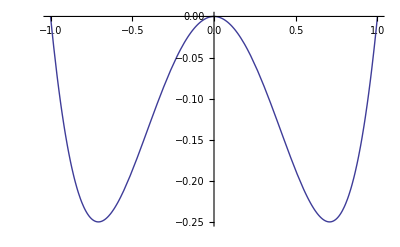

```mathematica
ϕ[s_,A_,C_]:=s^2*(A+C*s^2)
Plot[ϕ[x,-1,1],{x,-1,1}]
```

```mathematica
γ=(α+hα)//Simplify
γ=-γ/(Sqrt[2*α.p])//FullSimplify
(α.p)*(Outer[Times,γ,γ]-1/2*g)-Qfl//FullSimplify
```

{a1+(-a2 g11+a1 g12)/(√(-g12^2+g11 g22)),a2+(-a2 g12+a1 g22)/(√(-g12^2+g11 g22))}

{(a2 g11-a1 (g12+√(-g12^2+g11 g22)))/(√2 √((a2^2 g11-2 a1 a2 g12+a1^2 g22)/(-g12^2+g11 g22)) √(-g12^2+g11 g22)),(-a1 g22+a2 (g12-√(-g12^2+g11 g22)))/(√2 √((a2^2 g11-2 a1 a2 g12+a1^2 g22)/(-g12^2+g11 g22)) √(-g12^2+g11 g22))}

{{0,0},{0,0}}